```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,50,100,150,200,250,300,350,400,450,500,550,600,650,700};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>".dat"],{i,1,Length[mub]}];
```

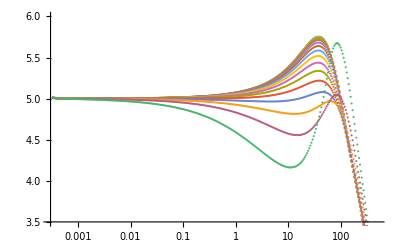

```mathematica
ListPlot[fitdata[[1;;-1]],PlotRange->{{3 10^-4,500},{3.5,6}},ScalingFunctions->{"Log"}]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]]],{i,1,Length[mub]}];
```

```mathematica
Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-5)/5]==0.02,{x,0.1}],2][[1]][[2]],{i,1,Length[mub]}]
```

InterpolatingFunction::dmval: 输入值 {-29.7938} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {-99.5325} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {-343.796} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

{1.52957,1.54064,1.57524,1.63823,1.73942,1.89778,2.15147,2.58511,3.41861,5.37695,11.7816,88.4001,1.86943,0.369264,0.063239}

```mathematica
Export["deltaregion.dat",%]
```

deltaregion.dat

```mathematica
Export["mub2.dat",mub]
```

mub2.dat

```mathematica
Log[{1.5295737850688516,1.5406354036702825,1.575243883656357,1.6382318335315784,1.7394199934281394,1.8977758285610413,2.151470883016552,2.5851130709592294,3.418611386548992,5.376948719201623,11.78159307835289,88.40010083250333,1.869430485405174,0.3692636292969653,0.06323896318792123}]
```

{0.424989,0.432195,0.45441,0.493618,0.553552,0.640683,0.766152,0.949769,1.22923,1.68212,2.46654,4.48187,0.625634,-0.996244,-2.76083}